Симеон Юруков  1901261094

# Изпит КЧМ

#### зад1

```mathematica
f[x_]:= (√(x^3)- 14*Sin[x])/(1+Cos[x]^2)-45
```

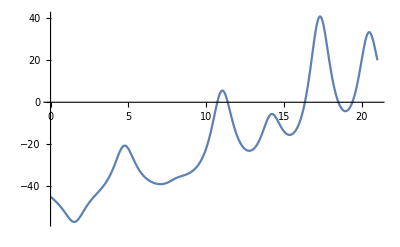

```mathematica
Plot[f[x],{x,0,21}]
```

Izvod: 5 Korena

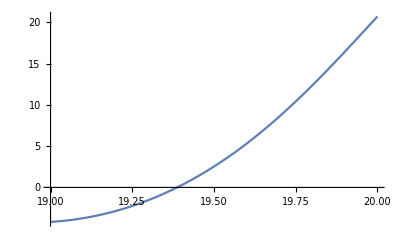

```mathematica
Plot[f[x],{x,19,20}]
```

```mathematica
f[19.]
```

-4.18114

```mathematica
f[20.]
```

20.7175

```mathematica
f[x_]:= (√(x^3)- 14*Sin[x])/(1+Cos[x]^2)-45
```

```mathematica
a = 19.; b = 20.;
```

```mathematica
For[n=0,n<=3, n++,
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2," f(m_n) = ",f[m]," ε_n = ",(b-a)/2];
If[f[m]>0,b=m,a=m]
]
```

n = 0 a_n = 19. b_n = 20. m_n = 19.5 f(m_n) = 2.53021 ε_n = 0.5

n = 1 a_n = 19. b_n = 19.5 m_n = 19.25 f(m_n) = -2.2511 ε_n = 0.25

n = 2 a_n = 19.25 b_n = 19.5 m_n = 19.375 f(m_n) = -0.238705 ε_n = 0.125

n = 3 a_n = 19.375 b_n = 19.5 m_n = 19.4375 f(m_n) = 1.0486 ε_n = 0.0625

```mathematica
f[x_]:= (√(x^3)- 14*Sin[x])/(1+Cos[x]^2)-45
```

```mathematica
a = 19.; b = 20.;
```

```mathematica
epszad = 0.0000001;
eps= Infinity; (*стойност по-голяма от зададената грешка*)
For[n=0,eps>epszad, n++,
Print["n = ",n," a_n = ",a," b_n = ",b," m_n = ",m = (a+b)/2," f(m_n) = ",f[m]," ε_n = ",eps = (b-a)/2];
If[f[m]>0,b=m,a=m]
]
```

n = 0 a_n = 19. b_n = 20. m_n = 19.5 f(m_n) = 2.53021 ε_n = 0.5

n = 1 a_n = 19. b_n = 19.5 m_n = 19.25 f(m_n) = -2.2511 ε_n = 0.25

n = 2 a_n = 19.25 b_n = 19.5 m_n = 19.375 f(m_n) = -0.238705 ε_n = 0.125

n = 3 a_n = 19.375 b_n = 19.5 m_n = 19.4375 f(m_n) = 1.0486 ε_n = 0.0625

n = 4 a_n = 19.375 b_n = 19.4375 m_n = 19.4063 f(m_n) = 0.380945 ε_n = 0.03125

n = 5 a_n = 19.375 b_n = 19.4063 m_n = 19.3906 f(m_n) = 0.0651594 ε_n = 0.015625

n = 6 a_n = 19.375 b_n = 19.3906 m_n = 19.3828 f(m_n) = -0.0882577 ε_n = 0.0078125

n = 7 a_n = 19.3828 b_n = 19.3906 m_n = 19.3867 f(m_n) = -0.011921 ε_n = 0.00390625

n = 8 a_n = 19.3867 b_n = 19.3906 m_n = 19.3887 f(m_n) = 0.0265262 ε_n = 0.00195313

n = 9 a_n = 19.3867 b_n = 19.3887 m_n = 19.3877 f(m_n) = 0.00727932 ε_n = 0.000976563

n = 10 a_n = 19.3867 b_n = 19.3877 m_n = 19.3872 f(m_n) = -0.00232666 ε_n = 0.000488281

n = 11 a_n = 19.3872 b_n = 19.3877 m_n = 19.3875 f(m_n) = 0.00247488 ε_n = 0.000244141

n = 12 a_n = 19.3872 b_n = 19.3875 m_n = 19.3873 f(m_n) = 0.0000737473 ε_n = 0.00012207

n = 13 a_n = 19.3872 b_n = 19.3873 m_n = 19.3873 f(m_n) = -0.00112655 ε_n = 0.0000610352

n = 14 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = -0.000526422 ε_n = 0.0000305176

n = 15 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = -0.000226343 ε_n = 0.0000152588

n = 16 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = -0.0000762993 ε_n = 7.62939×10^-6

n = 17 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = -1.27638×10^-6 ε_n = 3.8147×10^-6

n = 18 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = 0.0000362354 ε_n = 1.90735×10^-6

n = 19 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = 0.0000174795 ε_n = 9.53674×10^-7

n = 20 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = 8.10153×10^-6 ε_n = 4.76837×10^-7

n = 21 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = 3.41257×10^-6 ε_n = 2.38419×10^-7

n = 22 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = 1.0681×10^-6 ε_n = 1.19209×10^-7

n = 23 a_n = 19.3873 b_n = 19.3873 m_n = 19.3873 f(m_n) = -1.04144×10^-7 ε_n = 5.96046×10^-8

```mathematica
Log2[(20.-19.)/0.0000001]-1
```

22.2535

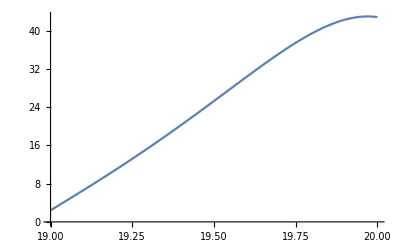

```mathematica
Plot[f'[x],{x,19.,20.}]
```

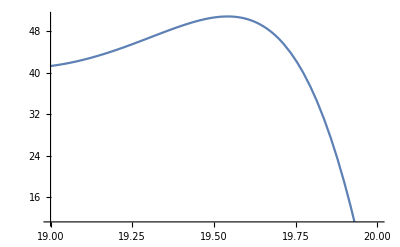

```mathematica
Plot[f''[x],{x,19.,20.}]
```

```mathematica
x0 = 19.
```

19.

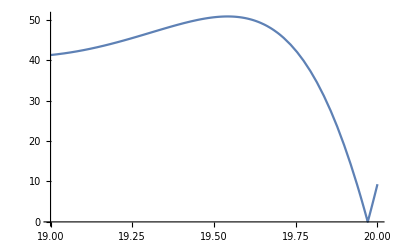

```mathematica
Plot[Abs[f''[x]],{x,19.,20.}]
```

```mathematica
M2 = Abs[f''[20.]]
```

9.33048

```mathematica
m1= Abs[f'[19.]]
```

2.42418

```mathematica
P = M2/(2 m1)
```

1.92446

```mathematica
f[x_]:= (√(x^3)- 14*Sin[x])/(1+Cos[x]^2)-45
x0 = 19.;
M2 = Abs[f''[20.]];
m1= Abs[f'[19.]];
P = M2/(2 m1);
epszad = 0.0000001;
eps= Infinity;
Print["n = ", 0, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0]]
For[n=0,eps >epszad, n++,
x1 = x0 -f[x0]/f'[x0];
eps = P*Abs[x1-x0]^2;
x0 = x1;
Print["n = ", n, " x_n = ", x0, " f(x_n) = ", f[x0], " f'(x_n) = ", f'[x0], " ε_n = ", eps]
]
```

n = 0 x_n = 19. f(x_n) = -4.18114 f'(x_n) = 2.42418

n = 0 x_n = 20.7248 f(x_n) = 29.3156 f'(x_n) = -28.8815 ε_n = 5.72489

n = 1 x_n = 21.7398 f(x_n) = 5.50297 f'(x_n) = -1.94961 ε_n = 1.98274

n = 2 x_n = 24.5624 f(x_n) = 30.6763 f'(x_n) = -42.8066 ε_n = 15.3323

n = 3 x_n = 25.279 f(x_n) = 18.2003 f'(x_n) = 6.02293 ε_n = 0.988312

n = 4 x_n = 22.2572 f(x_n) = 11.2876 f'(x_n) = 25.4495 ε_n = 17.5731

n = 5 x_n = 21.8137 f(x_n) = 5.49152 f'(x_n) = 1.64363 ε_n = 0.378578

n = 6 x_n = 18.4726 f(x_n) = 0.346913 f'(x_n) = -20.1732 ε_n = 21.4826

n = 7 x_n = 18.4898 f(x_n) = 0.00701639 f'(x_n) = -19.3585 ε_n = 0.000569117

n = 8 x_n = 18.4901 f(x_n) = 3.09693×10^-6 f'(x_n) = -19.3414 ε_n = 2.5281×10^-7

n = 9 x_n = 18.4901 f(x_n) = 5.8975×10^-13 f'(x_n) = -19.3414 ε_n = 4.93397×10^-14

## Zad 2

```mathematica
A = ({{1+2/7, 0.05, -0.1}, {0.2, 1-1/11, 0}, {0.5, 0, 1+3/13}}); b = {9,5,5};
Print["За сравнение, точното решение е ", LinearSolve[A,b]]
```

За сравнение, точното решение е {6.94213,3.97273,1.24226}

```mathematica
n = Length[A];
IM = IdentityMatrix[n];
B = IM-A;
c = b;
Print["Итерационният процес е x^(k + 1) = ", B//MatrixForm, ". x^(k) + ", c//MatrixForm]
```

Итерационният процес е x^(k + 1) = (-2/7 | -0.05 | 0.1
-0.2 | 1/11 | 0
-0.5 | 0 | -3/13). x^(k) + (9
5
5)

## Normi

```mathematica
Max[Table[∑_(j=1)^n Abs[B[[i,j]]],{i,n}]] (*purva*)
```

0.730769

```mathematica
Max[Table[∑_(i=1)^n Abs[B[[i,j]]],{j,n}]] (*vtora*)
```

0.985714

```mathematica
√(∑_(i=1)^n ∑_(j=1)^n B[[i,j]]^2) (*treta*)
```

0.667571

```mathematica
A = ({{1+2/7, 0.05, -0.1}, {0.2, 1-1/11, 0}, {0.5, 0, 1+3/13}}); b = {9,5,5};
Print["За сравнение, точното решение е ", LinearSolve[A,b]]
```

За сравнение, точното решение е {6.94213,3.97273,1.24226}

```mathematica
n = Length[A];
IM = IdentityMatrix[n];
B = IM-A;
c = b;
Print["Итерационният процес е x^(k + 1) = ", B//MatrixForm, ". x^(k) + ", c//MatrixForm]
```

Итерационният процес е x^(k + 1) = (-2/7 | -0.05 | 0.1
-0.2 | 1/11 | 0
-0.5 | 0 | -3/13). x^(k) + (9
5
5)

```mathematica
x = {6,1,15};
```

```mathematica
normB = √(∑_(i=1)^n ∑_(j=1)^n B[[i,j]]^2)
```

0.667571

```mathematica
normx0 = Norm[x,1];
normc = Norm[c,1];
For[k = 0, k<=5, k++,
Print["k = ", k, " x^(k) = ",x, " ε_k = ", eps = normB^k(normx0 +normc/(1-normB))];
x = B.x +c
]
```

k = 0 x^(k) = {6,1,15} ε_k = 79.1551

k = 1 x^(k) = {8.73571,3.89091,-1.46154} ε_k = 52.8417

k = 2 x^(k) = {6.16338,3.60658,0.969421} ε_k = 35.2756

k = 3 x^(k) = {7.15565,4.09519,1.6946} ε_k = 23.549

k = 4 x^(k) = {6.92023,3.94116,1.03112} ε_k = 15.7206

k = 5 x^(k) = {6.92885,3.97424,1.30194} ε_k = 10.4946

```mathematica
Log[10^-4/(normx0 +normc/(1-normB))]/Log[normB]
```

33.6091

```mathematica
Proverka
```

```mathematica
A = ({{1+2/7, 0.05, -0.1}, {0.2, 1-1/11, 0}, {0.5, 0, 1+3/13}}); b = {9,5,5};
Print["За сравнение, точното решение е ", LinearSolve[A,b]]
```

За сравнение, точното решение е {6.94213,3.97273,1.24226}

```mathematica
n = Length[A];
IM = IdentityMatrix[n];
B = IM-A;
c = b;
Print["Итерационният процес е x^(k + 1) = ", B//MatrixForm, ". x^(k) + ", c//MatrixForm]
```

Итерационният процес е x^(k + 1) = (-2/7 | -0.05 | 0.1
-0.2 | 1/11 | 0
-0.5 | 0 | -3/13). x^(k) + (9
5
5)

```mathematica
x = {6,1,15};
```

```mathematica
normB = √(∑_(i=1)^n ∑_(j=1)^n B[[i,j]]^2)
```

```mathematica
normx0 = Norm[x,1];
normc = Norm[c,1];
For[k = 0, k<=40, k++,
Print["k = ", k, " x^(k) = ",x, " ε_k = ", eps = normB^k(normx0 +normc/(1-normB))];
x = B.x +c
]
```

k = 0 x^(k) = {6,1,15} ε_k = 79.1551

k = 1 x^(k) = {8.73571,3.89091,-1.46154} ε_k = 52.8417

k = 2 x^(k) = {6.16338,3.60658,0.969421} ε_k = 35.2756

k = 3 x^(k) = {7.15565,4.09519,1.6946} ε_k = 23.549

k = 4 x^(k) = {6.92023,3.94116,1.03112} ε_k = 15.7206

k = 5 x^(k) = {6.92885,3.97424,1.30194} ε_k = 10.4946

k = 6 x^(k) = {6.95181,3.97553,1.23513} ε_k = 7.00592

k = 7 x^(k) = {6.9385,3.97105,1.23906} ε_k = 4.67695

k = 8 x^(k) = {6.94292,3.9733,1.24481} ε_k = 3.1222

k = 9 x^(k) = {6.94212,3.97262,1.24127} ε_k = 2.08429

k = 10 x^(k) = {6.94203,3.97272,1.24249} ε_k = 1.39141

k = 11 x^(k) = {6.94218,3.97275,1.24226} ε_k = 0.928868

k = 12 x^(k) = {6.94211,3.97272,1.24224} ε_k = 0.620086

k = 13 x^(k) = {6.94213,3.97273,1.24227} ε_k = 0.413951

k = 14 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.276342

k = 15 x^(k) = {6.94212,3.97273,1.24226} ε_k = 0.184478

k = 16 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.123152

k = 17 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0822129

k = 18 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.054883

k = 19 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0366383

k = 20 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0244587

k = 21 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0163279

k = 22 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0109001

k = 23 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00727657

k = 24 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00485763

k = 25 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00324281

k = 26 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00216481

k = 27 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00144516

k = 28 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00096475

k = 29 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00064404

k = 30 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.000429943

k = 31 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.000287017

k = 32 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.000191605

k = 33 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.00012791

k = 34 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000853889

k = 35 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000570032

k = 36 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000380537

k = 37 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000254036

k = 38 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000169587

k = 39 x^(k) = {6.94213,3.97273,1.24226} ε_k = 0.0000113211

k = 40 x^(k) = {6.94213,3.97273,1.24226} ε_k = 7.55766×10^-6

```mathematica
Log[10^-7/(normx0 +normc/(1-normB))]/Log[normB]
```

50.3745

```mathematica
Zad4
```

```mathematica
a = 0.; b = 0.5;
x = a;
y = 4.;
f[x_,y_]:= y-10*Sin[x];
```

```mathematica
n = 16;
```

```mathematica
h= (b-a)/n;
```

```mathematica
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y]];
y = y+h*f[x,y];
x=x+h
]
```

Мрежата е с n = 16 и стъпка h = 0.03125

Теоретичната локална  грешка е 0.000976563

Теоретичната глобална грешка е 0.03125

i = 0 x_i = 0. y_i = 4. f_i = 4.

i = 1 x_i = 0.03125 y_i = 4.125 f_i = 3.81255

i = 2 x_i = 0.0625 y_i = 4.24414 f_i = 3.61955

i = 3 x_i = 0.09375 y_i = 4.35725 f_i = 3.42113

i = 4 x_i = 0.125 y_i = 4.46416 f_i = 3.21742

i = 5 x_i = 0.15625 y_i = 4.56471 f_i = 3.00856

i = 6 x_i = 0.1875 y_i = 4.65872 f_i = 2.79469

i = 7 x_i = 0.21875 y_i = 4.74606 f_i = 2.57596

i = 8 x_i = 0.25 y_i = 4.82656 f_i = 2.35252

i = 9 x_i = 0.28125 y_i = 4.90007 f_i = 2.12451

i = 10 x_i = 0.3125 y_i = 4.96646 f_i = 1.89208

i = 11 x_i = 0.34375 y_i = 5.02559 f_i = 1.65539

i = 12 x_i = 0.375 y_i = 5.07732 f_i = 1.4146

i = 13 x_i = 0.40625 y_i = 5.12153 f_i = 1.16986

i = 14 x_i = 0.4375 y_i = 5.15809 f_i = 0.921325

i = 15 x_i = 0.46875 y_i = 5.18688 f_i = 0.669164

i = 16 x_i = 0.5 y_i = 5.20779 f_i = 0.413535

Tochno reshenie

### Obshto

```mathematica
Clear[x,y]
DSolve[y'[x]== y[x]-10*Sin[x], y[x],x]
```

{{y[x]→ⅇ^x C[1]+5 (Cos[x]+Sin[x])}}

## Chastno

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x]-10*Sin[x], y[0] == 4}, y[x],x]
```

{{y[x]→-ⅇ^x+5 Cos[x]+5 Sin[x]}}

```mathematica
yt[x_]:=-ⅇ^x+5 Cos[x]+5 Sin[x]
```

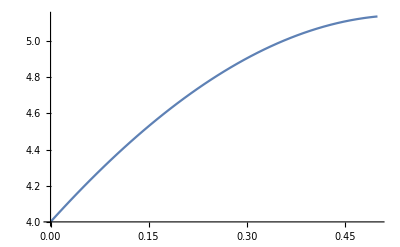

```mathematica
Plot[yt[x],{x,0.,0.5}]
```

## Modificiran Metod na OIler

```mathematica
a = 0.; b = 0.5;
x = a;
y = 4.;
f[x_,y_]:= y-10*Sin[x];
```

```mathematica
points = {{x,y}};
```

```mathematica
n = 16;
```

```mathematica
h= (b-a)/n;
```

```mathematica
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 16 и стъпка h = 0.03125

Теоретичната локална  грешка е 0.0000305176

Теоретичната глобална грешка е 0.000976563

i = 0 x_i = 0. y_i = 4. f_i = 4. x_(i + 1/2) = 0.015625 y_(i + 1/2) = 4.0625 f_(i + 1/2) = 3.90626 y_точно = 4. истинска грешка = 0.

i = 1 x_i = 0.03125 y_i = 4.12207 f_i = 3.80962 x_(i + 1/2) = 0.046875 y_(i + 1/2) = 4.1816 f_(i + 1/2) = 3.71302 y_точно = 4.12204 истинска грешка = 0.0000305563

i = 2 x_i = 0.0625 y_i = 4.2381 f_i = 3.61351 x_(i + 1/2) = 0.078125 y_(i + 1/2) = 4.29456 f_(i + 1/2) = 3.51411 y_точно = 4.23804 истинска грешка = 0.0000626239

i = 3 x_i = 0.09375 y_i = 4.34792 f_i = 3.41179 x_(i + 1/2) = 0.109375 y_(i + 1/2) = 4.40123 f_(i + 1/2) = 3.30966 y_точно = 4.34782 истинска грешка = 0.0000962306

i = 4 x_i = 0.125 y_i = 4.45134 f_i = 3.2046 x_(i + 1/2) = 0.140625 y_(i + 1/2) = 4.50142 f_(i + 1/2) = 3.0998 y_точно = 4.45121 истинска грешка = 0.000131405

i = 5 x_i = 0.15625 y_i = 4.54821 f_i = 2.99206 x_(i + 1/2) = 0.171875 y_(i + 1/2) = 4.59496 f_(i + 1/2) = 2.88466 y_точно = 4.54805 истинска грешка = 0.000168177

i = 6 x_i = 0.1875 y_i = 4.63836 f_i = 2.77433 x_(i + 1/2) = 0.203125 y_(i + 1/2) = 4.68171 f_(i + 1/2) = 2.6644 y_точно = 4.63815 истинска грешка = 0.000206576

i = 7 x_i = 0.21875 y_i = 4.72162 f_i = 2.55153 x_(i + 1/2) = 0.234375 y_(i + 1/2) = 4.76149 f_(i + 1/2) = 2.43914 y_точно = 4.72138 истинска грешка = 0.000246633

i = 8 x_i = 0.25 y_i = 4.79784 f_i = 2.32381 x_(i + 1/2) = 0.265625 y_(i + 1/2) = 4.83415 f_(i + 1/2) = 2.20903 y_точно = 4.79756 истинска грешка = 0.000288381

i = 9 x_i = 0.28125 y_i = 4.86688 f_i = 2.09131 x_(i + 1/2) = 0.296875 y_(i + 1/2) = 4.89955 f_(i + 1/2) = 1.97422 y_точно = 4.86655 истинска грешка = 0.000331852

i = 10 x_i = 0.3125 y_i = 4.92857 f_i = 1.85419 x_(i + 1/2) = 0.328125 y_(i + 1/2) = 4.95754 f_(i + 1/2) = 1.73486 y_точно = 4.92819 истинска грешка = 0.000377081

i = 11 x_i = 0.34375 y_i = 4.98279 f_i = 1.61259 x_(i + 1/2) = 0.359375 y_(i + 1/2) = 5.00798 f_(i + 1/2) = 1.49109 y_точно = 4.98236 истинска грешка = 0.000424103

i = 12 x_i = 0.375 y_i = 5.02938 f_i = 1.36666 x_(i + 1/2) = 0.390625 y_(i + 1/2) = 5.05074 f_(i + 1/2) = 1.24307 y_точно = 5.02891 истинска грешка = 0.000472953

i = 13 x_i = 0.40625 y_i = 5.06823 f_i = 1.11655 x_(i + 1/2) = 0.421875 y_(i + 1/2) = 5.08567 f_(i + 1/2) = 0.990957 y_точно = 5.0677 истинска грешка = 0.00052367

i = 14 x_i = 0.4375 y_i = 5.0992 f_i = 0.862433 x_(i + 1/2) = 0.453125 y_(i + 1/2) = 5.11267 f_(i + 1/2) = 0.734898 y_точно = 5.09862 истинска грешка = 0.000576293

i = 15 x_i = 0.46875 y_i = 5.12216 f_i = 0.604447 x_(i + 1/2) = 0.484375 y_(i + 1/2) = 5.13161 f_(i + 1/2) = 0.475052 y_точно = 5.12153 истинска грешка = 0.000630861

i = 16 x_i = 0.5 y_i = 5.13701 f_i = 0.342751 x_(i + 1/2) = 0.515625 y_(i + 1/2) = 5.14236 f_(i + 1/2) = 0.211575 y_точно = 5.13632 истинска грешка = 0.000687417

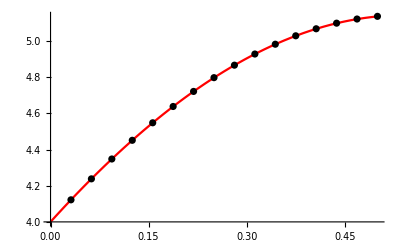

```mathematica
For[i = 0, i<= n, i++,
x12 = x+h/2;
y12 = y +h/2*f[x,y];
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " x_(i + 1/2) = ",x12, " y_(i + 1/2) = ",y12, " f_(i + 1/2) = ",f[x12,y12], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x12,y12];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,0.,0.5}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

## Zad3

```mathematica
xt = Table[9+q*(0.5),{q,-5,5}]
```

{6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5}

```mathematica
bigN = Length[xt]
```

11

```mathematica
f[x_]:=x-3*Cos[x]
```

```mathematica
yt = f[xt]
```

{3.57024,4.73829,6.46009,8.4365,10.306,11.7334,12.4915,12.5172,11.9266,10.9867,10.0501}

```mathematica
xt^2
```

{42.25,49.,56.25,64.,72.25,81.,90.25,100.,110.25,121.,132.25}

```mathematica
yt*xt
```

{23.2065,33.1681,48.4507,67.492,87.6013,105.601,118.669,125.172,125.229,120.854,115.576}

```mathematica
xt^3
```

{274.625,343.,421.875,512.,614.125,729.,857.375,1000.,1157.63,1331.,1520.88}

```mathematica
xt^4
```

{1785.06,2401.,3164.06,4096.,5220.06,6561.,8145.06,10000.,12155.1,14641.,17490.1}

```mathematica
yt*xt^2
```

{150.843,232.176,363.38,539.936,744.611,950.405,1127.36,1251.72,1314.91,1329.39,1329.12}

```mathematica
∑_(i=1)^bigN xt[[i]]
```

99.

```mathematica
∑_(i=1)^bigN yt[[i]]
```

103.217

```mathematica
∑_(i=1)^bigN xt[[i]]^2
```

918.5

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]
```

971.02

```mathematica
∑_(i=1)^bigN xt[[i]]^3
```

8761.5

```mathematica
∑_(i=1)^bigN xt[[i]]^4
```

85658.4

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]^2
```

9333.86

```mathematica
A = ({{11, 99., 918.5}, {99., 918.5, 8761.5}, {918.5, 8761.5, 85658.4}}); b = {103.217, 971.02, 9333.86};
LinearSolve[A,b]
```

{-65.7874,15.6095,-0.782209}

```mathematica
P2[x_]:=-0.782209 x^2+ 15.6095 x -65.7874
```

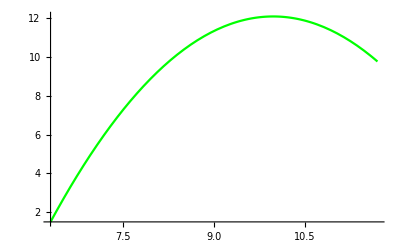

```mathematica
grP2 =Plot[P2[x],{x,xt[[1]]-0.2,xt[[bigN]]+0.2}, PlotStyle->Green]
```